```mathematica
storm="floyd";
grid="fine";
If[grid=="fine",node=254896];
outfilename="ds_bc.csv";
usname="rivers_on";
dsname="fine_grid";
```

```mathematica
If[storm=="irene",
boundaries={"Tarboro","Greenville","Pamlico", "Rock Springs", "Grimesland"};
stormnames={"spinup", "hurricane", "spindown"};
rbase="D:\\Dropbox\\irene_norivers\\";
];

If[storm=="april2003"∨storm=="april2003_norivers",
boundaries={(*"Tarboro","Greenville",*)"Pamlico"};
stormnames={"riverless results"(*,"river results"*)};
rbase="D:\\Dropbox\\april2003\\";
];

If[storm=="isabel",
boundaries={"Tarboro","Greenville","Pamlico"};
stormnames={"spinup","hurricane","spindown"};
rbase="D:\\Dropbox\\isabel\\";
];

If[storm=="floyd",
boundaries={"Tarboro","Greenville","Pamlico"};
stormnames={"spinup","hurricane","spindown"};
rbase="D:\\Dropbox\\floyd\\";
];

If[storm=="floyd_norivers",
boundaries={"Tarboro","Greenville","Pamlico"};
stormnames={"spinup","hurricane","spindown"};
rbase="D:\\Dropbox\\floyd_norivers\\";
];

If[storm=="april2003",
datestart=AbsoluteTime["March 15, 2003"];
];

If[storm=="irene",
datestart=AbsoluteTime["August 20, 2011"]-(24*60*60*45);
];

If[storm=="floyd"∨storm=="floyd_norivers",
datestart=AbsoluteTime["September 11, 1999"]-(24*60*60*31);
];
```

```mathematica
list63=Table[StringJoin[rbase,stormnames[[i]],"\\fort.63"],{i,1,Length[stormnames]}]
```

{D:\Dropbox\floyd\spinup\fort.63,D:\Dropbox\floyd\hurricane\fort.63,D:\Dropbox\floyd\spindown\fort.63}

```mathematica
(*find length of arrays*)
length63=0;
Do[
s=OpenRead[list63[[i]]];
Skip[s,String];
length63=length63+Read[s,Number];
Close[s];
,{i,1,Length[list63]}];


(*populate arrays*)
wses=Table[na,{length}];
validate=wses;
times=wses;

index=1;
Do[
Print[i];
s=OpenRead[list63[[i]]];
Skip[s,String];
NDSETSE=Read[s,Number];
NP=Read[s,Number];
Skip[s,String];
times[[index]]=Read[s,Number];
Skip[s,String,node];
validate[[index]]=Read[s,Number];
wses[[index]]=Read[s,Number];
index++;

Do[
Skip[s,String,NP-node];
times[[index]]=Read[s,Number];
Skip[s,String,node];
validate[[index]]=Read[s,Number];
wses[[index]]=Read[s,Number];
index++;
Print[j];
,{j,2,NDSETSE}];



Close[s];
,{i,1,Length[list63]}];
```

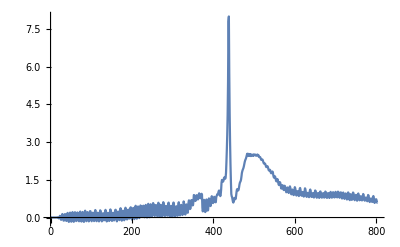

```mathematica
ListPlot[wses*3.28084,Joined->True, PlotRange->Full]
```

```mathematica
exlist1={
event,
"a1",
"adcirc",
usname,
dsname,
"washington",
"date_time",
"days_after_jan1_1900",(*in excel format*)
(times+datestart)/86400+2};
exlist1=Flatten[exlist1];


exlist2={
event,
"a1",
"adcirc",
usname,
dsname,
"washington",
"stage",
"ft_above_NAVD88",
wses*3.28084};
exlist2=Flatten[exlist2];

exlist=Transpose[Table[{exlist1,exlist2}]];

Export[StringJoin[rbase,outfilename],exlist];
```

```mathematica
exlist
```

{{event,event},{a1,a1},{adcirc,adcirc},{rivers_on,rivers_on},{fine_grid,fine_grid},{washington,washington},{date_time,stage},{days_after_jan1_1900,ft_above_NAVD88},{36383.1,-8.97246×10^-28},{36383.2,0.00596823},{36383.3,0.0044377},{36383.3,0.000196894},{36383.4,-0.00178159},{36383.5,-0.00126277},{36383.6,0.00128601},{36383.7,0.00213511},{36383.8,-0.00165601},{36383.8,0.000262075},{36383.9,0.00133974},{36384.,0.000214222},{36384.1,-0.000425904},{36384.2,-0.0000627526},{36384.3,0.000603775},{36384.3,0.00273951},{36384.4,0.00927794},{36384.5,0.00241747},{36384.6,-0.0144793},{36384.7,-0.0298172},{36384.8,-0.0350317},{36384.8,0.0149779},{36384.9,0.0675068},{36385.,0.0500633},{36385.1,-0.0262438},{36385.2,-0.0933684},{36385.3,-0.058336},{36385.3,0.0490103},{36385.4,0.140497},{36385.5,0.102854},{36385.6,-0.008983},{36385.7,-0.122756},{36385.8,-0.122961},{36385.8,0.00584328},{36385.9,0.133294},{36386.,0.135277},{36386.1,0.0191509},{36386.2,-0.115585},{36386.3,-0.136567},{36386.3,-0.00277703},{36386.4,0.149139},{36386.5,0.18506},{36386.6,0.0636834},{36386.7,-0.0893096},{36386.8,-0.173741},{36386.8,-0.0515501},{36386.9,0.110493},{36387.,0.196338},{36387.1,0.0983903},{36387.2,-0.0564227},{36387.3,-0.166323},{36387.3,-0.0638632},{36387.4,0.102497},{36387.5,0.215719},{36387.6,0.129619},{36387.7,-0.0248659},{36387.8,-0.169405},{36387.8,-0.103697},{36387.9,0.0621678},{36388.,0.213523},{36388.1,0.169316},{36388.2,0.0218151},{36388.3,-0.141186},{36388.3,-0.121759},{36388.4,0.0356249},{36388.5,0.202508},{36388.6,0.186373},{36388.7,0.0462084},{36388.8,-0.126887},{36388.8,-0.150215},{36388.9,0.00602179},{36389.,0.192197},{36389.1,0.237553},{36389.2,0.102667},{36389.3,-0.0738139},{36389.3,-0.160177},{36389.4,-0.028916},{36389.5,0.152428},{36389.6,0.220849},{36389.7,0.10799},{36389.8,-0.0655052},{36389.8,-0.173133},{36389.9,-0.042961},{36390.,0.144684},{36390.1,0.272338},{36390.2,0.176166},{36390.3,0.0106092},{36390.3,-0.145351},{36390.4,-0.0898269},{36390.5,0.076974},{36390.6,0.216267},{36390.7,0.15817},{36390.8,0.00449533},{36390.8,-0.153277},{36390.9,-0.0915766},{36391.,0.0796499},{36391.1,0.255737},{36391.2,0.250539},{36391.3,0.0961918},{36391.3,-0.0822992},{36391.4,-0.147661},{36391.5,-0.00599863},{36391.6,0.164667},{36391.7,0.192996},{36391.8,0.0712231},{36391.8,-0.099557},{36391.9,-0.143155},{36392.,0.0113314},{36392.1,0.203417},{36392.2,0.298364},{36392.3,0.17224},{36392.3,-0.00093072},{36392.4,-0.145743},{36392.5,-0.0820349},{36392.6,0.0797373},{36392.7,0.191361},{36392.8,0.129131},{36392.8,-0.0268046},{36392.9,-0.153711},{36393.,-0.0449757},{36393.1,0.130439},{36393.2,0.288872},{36393.3,0.245467},{36393.3,0.0848181},{36393.4,-0.0908514},{36393.5,-0.151805},{36393.6,-0.00591932},{36393.7,0.151737},{36393.8,0.170769},{36393.8,0.0491969},{36393.9,-0.110939},{36394.,-0.102754},{36394.1,0.0517578},{36394.2,0.241682},{36394.3,0.305355},{36394.3,0.16241},{36394.4,-0.0160787},{36394.5,-0.155329},{36394.6,-0.0741912},{36394.7,0.0867807},{36394.8,0.187941},{36394.8,0.125954},{36394.9,-0.0365178},{36395.,-0.137673},{36395.1,-0.0111237},{36395.2,0.176143},{36395.3,0.321828},{36395.3,0.234493},{36395.4,0.0710266},{36395.5,-0.112237},{36395.6,-0.135289},{36395.7,0.0246573},{36395.8,0.18479},{36395.8,0.188684},{36395.9,0.0492214},{36396.,-0.115472},{36396.1,-0.0599592},{36396.2,0.104244},{36396.3,0.300809},{36396.3,0.309147},{36396.4,0.160183},{36396.5,-0.0382736},{36396.6,-0.152317},{36396.7,-0.0201174},{36396.8,0.162365},{36396.8,0.236854},{36396.9,0.143308},{36397.,-0.0411937},{36397.1,-0.105134},{36397.2,0.0416891},{36397.3,0.25773},{36397.3,0.370036},{36397.4,0.245664},{36397.5,0.0542359},{36397.6,-0.12428},{36397.7,-0.0513335},{36397.8,0.127},{36397.8,0.274122},{36397.9,0.232856},{36398.,0.0550835},{36398.1,-0.108497},{36398.2,0.000537772},{36398.3,0.203326},{36398.3,0.390293},{36398.4,0.326779},{36398.5,0.160381},{36398.6,-0.0545386},{36398.7,-0.0781767},{36398.8,0.0938556},{36398.8,0.296384},{36398.9,0.312563},{36399.,0.166639},{36399.1,-0.0420694},{36399.2,-0.033607},{36399.3,0.141591},{36399.3,0.37329},{36399.4,0.408286},{36399.5,0.2712},{36399.6,0.038532},{36399.7,-0.083051},{36399.8,0.0674706},{36399.8,0.291626},{36399.9,0.381659},{36400.,0.287023},{36400.1,0.0630196},{36400.2,-0.061462},{36400.3,0.0930985},{36400.3,0.333149},{36400.4,0.468169},{36400.5,0.364837},{36400.6,0.148611},{36400.7,-0.0465317},{36400.8,0.0482259},{36400.8,0.264448},{36400.9,0.43916},{36401.,0.385551},{36401.1,0.186943},{36401.2,-0.0227139},{36401.3,0.056978},{36401.3,0.269724},{36401.4,0.481305},{36401.5,0.440497},{36401.6,0.265993},{36401.7,0.0297256},{36401.8,0.0222099},{36401.8,0.221883},{36401.9,0.457701},{36402.,0.470219},{36402.1,0.31908},{36402.2,0.0750704},{36402.3,0.0103654},{36402.3,0.197441},{36402.4,0.443263},{36402.5,0.50249},{36402.6,0.373775},{36402.7,0.128726},{36402.8,0.000707096},{36402.8,0.177596},{36402.9,0.426992},{36403.,0.545617},{36403.1,0.433641},{36403.2,0.198099},{36403.3,0.0116161},{36403.3,0.136422},{36403.4,0.368391},{36403.5,0.528686},{36403.6,0.450074},{36403.7,0.2356},{36403.8,0.0298396},{36403.8,0.130999},{36403.9,0.361166},{36404.,0.574889},{36404.1,0.512522},{36404.2,0.325617},{36404.3,0.0917652},{36404.3,0.0607687},{36404.4,0.266908},{36404.5,0.491945},{36404.6,0.494677},{36404.7,0.334769},{36404.8,0.10211},{36404.8,0.0575611},{36404.9,0.270255},{36405.,0.522116},{36405.1,0.588853},{36405.2,0.438009},{36405.3,0.200217},{36405.3,0.0330109},{36405.4,0.167008},{36405.5,0.388335},{36405.6,0.506482},{36405.7,0.419717},{36405.8,0.195232},{36405.8,0.0275208},{36405.9,0.177717},{36406.,0.415323},{36406.1,0.609926},{36406.2,0.515859},{36406.3,0.325111},{36406.3,0.100586},{36406.4,0.0574083},{36406.5,0.26213},{36406.6,0.460873},{36406.7,0.459903},{36406.8,0.295414},{36406.8,0.0839051},{36406.9,0.0723947},{36407.,0.286933},{36407.1,0.529463},{36407.2,0.593641},{36407.3,0.435629},{36407.3,0.20685},{36407.4,0.035467},{36407.5,0.142842},{36407.6,0.348753},{36407.7,0.466674},{36407.8,0.393272},{36407.8,0.186578},{36407.9,0.0225941},{36408.,0.173479},{36408.1,0.39942},{36408.2,0.596714},{36408.3,0.514491},{36408.3,0.334626},{36408.4,0.11227},{36408.5,0.0348071},{36408.6,0.23135},{36408.7,0.430625},{36408.8,0.449184},{36408.8,0.316529},{36408.9,0.106203},{36409.,0.0681553},{36409.1,0.280549},{36409.2,0.524976},{36409.3,0.607368},{36409.3,0.459242},{36409.4,0.259899},{36409.5,0.0845917},{36409.6,0.15824},{36409.7,0.365852},{36409.8,0.50319},{36409.8,0.439821},{36409.9,0.267374},{36410.,0.100197},{36410.1,0.20648},{36410.2,0.434374},{36410.3,0.640413},{36410.3,0.566928},{36410.4,0.426147},{36410.5,0.236317},{36410.6,0.119887},{36410.7,0.274072},{36410.8,0.505141},{36410.8,0.521803},{36410.9,0.422758},{36411.,0.250933},{36411.1,0.189849},{36411.2,0.334778},{36411.3,0.60653},{36411.3,0.683848},{36411.4,0.59399},{36411.5,0.456274},{36411.6,0.339641},{36411.7,0.400352},{36411.8,0.566241},{36411.8,0.695068},{36411.9,0.683398},{36412.,0.593301},{36412.1,0.482805},{36412.2,0.495149},{36412.3,0.650523},{36412.3,0.894697},{36412.4,0.888929},{36412.5,0.823081},{36412.6,0.713027},{36412.7,0.658132},{36412.8,0.72654},{36412.8,0.85932},{36412.9,0.889639},{36413.,0.853149},{36413.1,0.768386},{36413.2,0.718014},{36413.3,0.762437},{36413.3,0.905215},{36413.4,0.96391},{36413.5,0.926152},{36413.6,0.857732},{36413.7,0.772041},{36413.8,0.767614},{36413.8,0.865655},{36413.9,0.945158},{36414.,0.916482},{36414.1,0.38386},{36414.2,0.244262},{36414.3,0.352346},{36414.3,0.603412},{36414.4,0.704797},{36414.5,0.610613},{36414.6,0.417586},{36414.7,0.216791},{36414.8,0.276611},{36414.8,0.528831},{36414.9,0.717972},{36415.,0.653605},{36415.1,0.484592},{36415.2,0.277945},{36415.3,0.294021},{36415.3,0.505557},{36415.4,0.761532},{36415.5,0.734352},{36415.6,0.6302},{36415.7,0.490574},{36415.8,0.455232},{36415.8,0.551548},{36415.9,0.76519},{36416.,0.849306},{36416.1,0.788768},{36416.2,0.664983},{36416.3,0.574186},{36416.3,0.606093},{36416.4,0.732854},{36416.5,0.825886},{36416.6,0.773307},{36416.7,0.682132},{36416.8,0.607406},{36416.8,0.611743},{36416.9,0.801989},{36417.,0.863015},{36417.1,0.890395},{36417.2,0.934426},{36417.3,0.907565},{36417.3,0.984899},{36417.4,1.04853},{36417.5,1.07576},{36417.6,0.994641},{36417.7,0.910136},{36417.8,0.85117},{36417.8,0.926206},{36417.9,1.10403},{36418.,1.38519},{36418.1,1.49486},{36418.2,1.48799},{36418.3,1.42248},{36418.3,1.43388},{36418.4,1.4765},{36418.5,1.57479},{36418.6,1.59919},{36418.7,1.58267},{36418.8,1.54169},{36418.8,1.58599},{36418.9,1.7727},{36419.,2.18956},{36419.1,2.68658},{36419.2,3.28113},{36419.3,4.08659},{36419.3,5.3938},{36419.4,7.79847},{36419.5,8.00098},{36419.6,5.69696},{36419.7,4.10344},{36419.8,2.97542},{36419.8,2.10861},{36419.9,1.45334},{36420.,0.939702},{36420.1,0.846277},{36420.2,0.809692},{36420.3,0.716841},{36420.3,0.633335},{36420.4,0.595305},{36420.5,0.636415},{36420.6,0.75771},{36420.7,0.780226},{36420.8,0.75474},{36420.8,0.72597},{36420.9,0.769943},{36421.,0.89399},{36421.1,1.03296},{36421.2,1.12502},{36421.3,1.12391},{36421.3,1.09471},{36421.4,1.07733},{36421.5,1.11189},{36421.6,1.19618},{36421.7,1.307},{36421.8,1.38217},{36421.8,1.41852},{36421.9,1.45377},{36422.,1.52047},{36422.1,1.63851},{36422.2,1.7738},{36422.3,1.84257},{36422.3,1.89654},{36422.4,1.93513},{36422.5,1.98183},{36422.6,2.05038},{36422.7,2.13321},{36422.8,2.2131},{36422.8,2.27357},{36422.9,2.31193},{36423.,2.35319},{36423.1,2.40873},{36423.2,2.47764},{36423.3,2.53593},{36423.3,2.50972},{36423.4,2.53782},{36423.5,2.45197},{36423.6,2.51105},{36423.7,2.45457},{36423.8,2.52882},{36423.8,2.45753},{36423.9,2.50933},{36424.,2.44487},{36424.1,2.45291},{36424.2,2.50569},{36424.3,2.4762},{36424.3,2.46819},{36424.4,2.45959},{36424.5,2.50805},{36424.6,2.46107},{36424.7,2.49783},{36424.8,2.50504},{36424.8,2.50905},{36424.9,2.49585},{36425.,2.47164},{36425.1,2.45743},{36425.2,2.46432},{36425.3,2.49623},{36425.3,2.50807},{36425.4,2.49656},{36425.5,2.46345},{36425.6,2.4749},{36425.7,2.40861},{36425.8,2.40742},{36425.8,2.412},{36425.9,2.40077},{36426.,2.36037},{36426.1,2.31323},{36426.2,2.28837},{36426.3,2.30047},{36426.3,2.3136},{36426.4,2.29328},{36426.5,2.2472},{36426.6,2.18962},{36426.7,2.15134},{36426.8,2.14227},{36426.8,2.15306},{36426.9,2.14204},{36427.,2.1005},{36427.1,2.04208},{36427.2,2.00585},{36427.3,2.01147},{36427.3,2.04487},{36427.4,2.04033},{36427.5,2.00181},{36427.6,1.9328},{36427.7,1.87976},{36427.8,1.86764},{36427.8,1.8962},{36427.9,1.89877},{36428.,1.86287},{36428.1,1.78754},{36428.2,1.7612},{36428.3,1.78079},{36428.3,1.7794},{36428.4,1.83151},{36428.5,1.80261},{36428.6,1.70081},{36428.7,1.61834},{36428.8,1.58533},{36428.8,1.62058},{36428.9,1.6412},{36429.,1.61237},{36429.1,1.53417},{36429.2,1.45724},{36429.3,1.43751},{36429.3,1.4886},{36429.4,1.53185},{36429.5,1.50917},{36429.6,1.42215},{36429.7,1.32882},{36429.8,1.29186},{36429.8,1.34045},{36429.9,1.40904},{36430.,1.39671},{36430.1,1.3187},{36430.2,1.20535},{36430.3,1.15007},{36430.3,1.1963},{36430.4,1.28613},{36430.5,1.28552},{36430.6,1.20888},{36430.7,1.1261},{36430.8,1.09205},{36430.8,1.16061},{36430.9,1.26562},{36431.,1.23783},{36431.1,1.17493},{36431.2,1.06919},{36431.3,1.00473},{36431.3,1.03212},{36431.4,1.15504},{36431.5,1.19575},{36431.6,1.14594},{36431.7,1.03406},{36431.8,0.975793},{36431.8,1.03142},{36431.9,1.19384},{36432.,1.24048},{36432.1,1.18394},{36432.2,1.05547},{36432.3,0.933569},{36432.3,0.924918},{36432.4,1.0258},{36432.5,1.11324},{36432.6,1.09496},{36432.7,0.987608},{36432.8,0.89324},{36432.8,0.905241},{36432.9,1.04475},{36433.,1.20942},{36433.1,1.16949},{36433.2,1.06786},{36433.3,0.940965},{36433.3,0.874031},{36433.4,0.928286},{36433.5,1.03085},{36433.6,1.04971},{36433.7,0.963248},{36433.8,0.890985},{36433.8,0.853648},{36433.9,0.949443},{36434.,1.14574},{36434.1,1.17651},{36434.2,1.10716},{36434.3,0.971782},{36434.3,0.880152},{36434.4,0.866707},{36434.5,0.95646},{36434.6,1.01795},{36434.7,0.984273},{36434.8,0.907564},{36434.8,0.831716},{36434.9,0.875135},{36435.,1.04789},{36435.1,1.16315},{36435.2,1.12115},{36435.3,1.02015},{36435.3,0.891213},{36435.4,0.821494},{36435.5,0.883747},{36435.6,0.965243},{36435.7,0.983443},{36435.8,0.936067},{36435.8,0.827629},{36435.9,0.809576},{36436.,0.908753},{36436.1,1.07718},{36436.2,1.11484},{36436.3,1.04841},{36436.3,0.926487},{36436.4,0.820847},{36436.5,0.819781},{36436.6,0.910463},{36436.7,0.960378},{36436.8,0.978879},{36436.8,0.886208},{36436.9,0.794381},{36437.,0.825751},{36437.1,0.952133},{36437.2,1.0779},{36437.3,1.05311},{36437.3,0.945763},{36437.4,0.849591},{36437.5,0.786908},{36437.6,0.842131},{36437.7,0.936575},{36437.8,0.975236},{36437.8,0.925637},{36437.9,0.824173},{36438.,0.779866},{36438.1,0.851264},{36438.2,1.02833},{36438.3,1.03723},{36438.3,0.971305},{36438.4,0.893091},{36438.5,0.791648},{36438.6,0.797915},{36438.7,0.894691},{36438.8,0.961605},{36438.8,0.972026},{36438.9,0.893635},{36439.,0.791947},{36439.1,0.798542},{36439.2,0.908612},{36439.3,1.03459},{36439.3,0.99982},{36439.4,0.916242},{36439.5,0.830015},{36439.6,0.779384},{36439.7,0.845426},{36439.8,0.963161},{36439.8,0.972961},{36439.9,0.916026},{36440.,0.835553},{36440.1,0.77733},{36440.2,0.837051},{36440.3,0.979741},{36440.3,1.02024},{36440.4,0.960735},{36440.5,0.88849},{36440.6,0.789552},{36440.7,0.816365},{36440.8,0.936001},{36440.8,1.00911},{36440.9,0.970307},{36441.,0.903266},{36441.1,0.799455},{36441.2,0.804453},{36441.3,0.913619},{36441.3,1.0219},{36441.4,0.993387},{36441.5,0.924373},{36441.6,0.821133},{36441.7,0.80098},{36441.8,0.892157},{36441.8,1.0294},{36441.9,1.01539},{36442.,0.959027},{36442.1,0.832915},{36442.2,0.78585},{36442.3,0.85424},{36442.3,0.980052},{36442.4,1.00306},{36442.5,0.956341},{36442.6,0.826598},{36442.7,0.755229},{36442.8,0.810214},{36442.8,0.969633},{36442.9,0.994393},{36443.,0.940328},{36443.1,0.815691},{36443.2,0.742256},{36443.3,0.789486},{36443.3,0.896984},{36443.4,0.959589},{36443.5,0.916387},{36443.6,0.809685},{36443.7,0.716012},{36443.8,0.776989},{36443.8,0.908679},{36443.9,1.00027},{36444.,0.95414},{36444.1,0.845341},{36444.2,0.727335},{36444.3,0.691567},{36444.3,0.788912},{36444.4,0.929154},{36444.5,0.919834},{36444.6,0.820896},{36444.7,0.701978},{36444.8,0.725174},{36444.8,0.796674},{36444.9,0.996031},{36445.,0.965617},{36445.1,0.877885},{36445.2,0.742352},{36445.3,0.688789},{36445.3,0.760361},{36445.4,0.862565},{36445.5,0.90104},{36445.6,0.840316},{36445.7,0.723955},{36445.8,0.668216},{36445.8,0.781946},{36445.9,0.925076},{36446.,0.957347},{36446.1,0.887654},{36446.2,0.767483},{36446.3,0.68512},{36446.3,0.707541},{36446.4,0.79564},{36446.5,0.84908},{36446.6,0.823393},{36446.7,0.71003},{36446.8,0.680157},{36446.8,0.710723},{36446.9,0.843056},{36447.,0.937283},{36447.1,0.878084},{36447.2,0.777118},{36447.3,0.692185},{36447.3,0.670511},{36447.4,0.71888},{36447.5,0.793799},{36447.6,0.793586},{36447.7,0.704764},{36447.8,0.681703},{36447.8,0.647473},{36447.9,0.770532},{36448.,0.897529},{36448.1,0.875314},{36448.2,0.790893},{36448.3,0.675003},{36448.3,0.615724},{36448.4,0.646089},{36448.5,0.718069},{36448.6,0.758493},{36448.7,0.698844},{36448.8,0.68687},{36448.8,0.616701},{36448.9,0.687622},{36449.,0.822196},{36449.1,0.85452},{36449.2,0.782141},{36449.3,0.660396},{36449.3,0.579876},{36449.4,0.633739},{36449.5,0.66101},{36449.6,0.724111},{36449.7,0.727033},{36449.8,0.671778},{36449.8,0.59122},{36449.9,0.596856},{2+(3143318400+EndOfFile)/86400,3.28084 EndOfFile}}